# Verification of NAO Center of Mass

## Import Logs

### Center of Mass

```mathematica
FileAddress="D:/log_dance.txt";
Data = Import[FileAddress,"Data"];
lenData=Length[Data[[All,1]]];

readData = Function[len,
i+=len;
Data[[All,i-len;;i-1]]
];

i = 26;
comPython = readData[3];
comSensor = readData[3];
comHDPython =readData[3];
comHDSensor =readData[3];
comLHPython =readData[3];
comLHSensor =readData[3];
comRHPython =readData[3];
comRHSensor =readData[3];
comLLPython =readData[3];
comLLSensor =readData[3];
comRLPython =readData[3];
comRLSensor =readData[3];


setTheta=Function[i,
Subscript[θHD, 1]=Data[[i,2]];
Subscript[θHD, 2]=Data[[i,3]];

Subscript[θLH, 1]=Data[[i,4]];
Subscript[θLH, 2]=Data[[i,5]];
Subscript[θLH, 3]=Data[[i,6]];
Subscript[θLH, 4]=Data[[i,7]];
Subscript[θLH, 5]=Data[[i,8]];

Subscript[θRH, 1]=Data[[i,9]];
Subscript[θRH, 2]=Data[[i,10]];
Subscript[θRH, 3]=Data[[i,11]];
Subscript[θRH, 4]=Data[[i,12]];
Subscript[θRH, 5]=Data[[i,13]];

Subscript[θLL, 1]=Data[[i,14]];
Subscript[θLL, 2]=Data[[i,15]];
Subscript[θLL, 3]=Data[[i,16]];
Subscript[θLL, 4]=Data[[i,17]];
Subscript[θLL, 5]=Data[[i,18]];
Subscript[θLL, 6]=Data[[i,19]];

Subscript[θRL, 1]=Data[[i,20]];
Subscript[θRL, 2]=Data[[i,21]];
Subscript[θRL, 3]=Data[[i,22]];
Subscript[θRL, 4]=Data[[i,23]];
Subscript[θRL, 5]=Data[[i,24]];
Subscript[θRL, 6]=Data[[i,25]];
];
```

## Head

```mathematica
DHPHead:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θHD, 1]}, {0, 0, 0, Subscript[θHD, 2]}});

aah := DHPHead[[2;;-1,1]];
bh := DHPHead[[2;;-1,2]];
αh := DHPHead[[2;;-1,3]];
θh:= DHPHead[[2;;-1,4]];


qh[i_]:=({{Cos[θh[[i]]], -Cos[αh [[i]]]Sin[θh[[i]]], Sin[αh [[i]]]Sin[θh[[i]]]}, {Sin[θh[[i]]], Cos[αh [[i]]]Cos[θh[[i]]], -Sin[αh [[i]]]Cos[θh[[i]]]}, {0, Sin[αh[[i]]], Cos[αh[[i]]]}});

ah[i_]:=({{aah[[i]]Cos[θh[[i]]]}, {aah[[i]]Sin[θh[[i]]]}, {bh[[i]]}});

QHD2to1:=qh[1];
PHD2to1:=ah[1];
THD2to1:=({{QHD2to1[[1,1]], QHD2to1[[1,2]], QHD2to1[[1,3]], PHD2to1[[1,1]]}, {QHD2to1[[2,1]], QHD2to1[[2,2]], QHD2to1[[2,3]], PHD2to1[[2,1]]}, {QHD2to1[[3,1]], QHD2to1[[3,2]], QHD2to1[[3,3]], PHD2to1[[3,1]]}, {0, 0, 0, 1}});
QHD3to1:=qh[1].qh[2];
PHD3to1:=ah[1]+qh[1].ah[2];
THD3to1:=({{QHD3to1[[1,1]], QHD3to1[[1,2]], QHD3to1[[1,3]], PHD3to1[[1,1]]}, {QHD3to1[[2,1]], QHD3to1[[2,2]], QHD3to1[[2,3]], PHD3to1[[2,1]]}, {QHD3to1[[3,1]], QHD3to1[[3,2]], QHD3to1[[3,3]], PHD3to1[[3,1]]}, {0, 0, 0, 1}});
THD1toTorso:=({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0.1265}, {0, 0, 0, 1}});
THD3toTorso:=THD1toTorso.THD3to1;
```

## Left Hand

```mathematica
DHPLH:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θLH, 1]}, {Subscript[lh, 1], 0, π/2, Subscript[θLH, 2]+π/2}, {0, Subscript[lh, 2], π/2, Subscript[θLH, 3]+π}, {0, 0, π/2, Subscript[θLH, 4]+π}, {0, Subscript[lh, 3], 0, Subscript[θLH, 5]}})

Subscript[lh, 1]=0.015;
Subscript[lh, 2]=0.105;
Subscript[lh, 3]=0.05595;

aalh := DHPLH[[2;;-1,1]];
blh := DHPLH[[2;;-1,2]];
αlh := DHPLH[[2;;-1,3]];
θlh := DHPLH[[2;;-1,4]];

qLH[i_]:=({{Cos[θlh[[i]]], -Cos[αlh [[i]]]Sin[θlh[[i]]], Sin[αlh [[i]]]Sin[θlh[[i]]]}, {Sin[θlh[[i]]], Cos[αlh [[i]]]Cos[θlh[[i]]], -Sin[αlh [[i]]]Cos[θlh[[i]]]}, {0, Sin[αlh[[i]]], Cos[αlh[[i]]]}});

aLH[i_]:=({{aalh[[i]]Cos[θlh[[i]]]}, {aalh[[i]]Sin[θlh[[i]]]}, {blh[[i]]}});

QLH6to1:=qLH[1].qLH[2].qLH[3].qLH[4].qLH[5];
PLH6to1:=aLH[1]+qLH[1].aLH[2]+qLH[1].qLH[2].aLH[3]+qLH[1].qLH[2].qLH[3].aLH[4]+qLH[1].qLH[2].qLH[3].qLH[4].aLH[5];
TLH6to1:=({{QLH6to1[[1,1]], QLH6to1[[1,2]], QLH6to1[[1,3]], PLH6to1[[1,1]]}, {QLH6to1[[2,1]], QLH6to1[[2,2]], QLH6to1[[2,3]], PLH6to1[[2,1]]}, {QLH6to1[[3,1]], QLH6to1[[3,2]], QLH6to1[[3,3]], PLH6to1[[3,1]]}, {0, 0, 0, 1}});
TLH1toTorso= ({{1, 0, 0, 0}, {0, 0, 1, 0.098}, {0, -1, 0, 0.100}, {0, 0, 0, 1}});
TLH6toTorso:=TLH1toTorso.TLH6to1;

QLH2to1:=qLH[1];
PLH2to1:=aLH[1];
TLH2to1:=({{QLH2to1[[1,1]], QLH2to1[[1,2]], QLH2to1[[1,3]], PLH2to1[[1,1]]}, {QLH2to1[[2,1]], QLH2to1[[2,2]], QLH2to1[[2,3]], PLH2to1[[2,1]]}, {QLH2to1[[3,1]], QLH2to1[[3,2]], QLH2to1[[3,3]], PLH2to1[[3,1]]}, {0, 0, 0, 1}});
QLH3to1:=qLH[1].qLH[2];
PLH3to1:=aLH[1]+qLH[1].aLH[2];
TLH3to1:=({{QLH3to1[[1,1]], QLH3to1[[1,2]], QLH3to1[[1,3]], PLH3to1[[1,1]]}, {QLH3to1[[2,1]], QLH3to1[[2,2]], QLH3to1[[2,3]], PLH3to1[[2,1]]}, {QLH3to1[[3,1]], QLH3to1[[3,2]], QLH3to1[[3,3]], PLH3to1[[3,1]]}, {0, 0, 0, 1}});
QLH4to1:=qLH[1].qLH[2].qLH[3];
PLH4to1:=aLH[1]+qLH[1].aLH[2]+qLH[1].qLH[2].aLH[3];
TLH4to1:=({{QLH4to1[[1,1]], QLH4to1[[1,2]], QLH4to1[[1,3]], PLH4to1[[1,1]]}, {QLH4to1[[2,1]], QLH4to1[[2,2]], QLH4to1[[2,3]], PLH4to1[[2,1]]}, {QLH4to1[[3,1]], QLH4to1[[3,2]], QLH4to1[[3,3]], PLH4to1[[3,1]]}, {0, 0, 0, 1}});

QLH5to1:=qLH[1].qLH[2].qLH[3].qLH[4];
PLH5to1:=aLH[1]+qLH[1].aLH[2]+qLH[1].qLH[2].aLH[3]+qLH[1].qLH[2].qLH[3].aLH[4];
TLH5to1:=({{QLH5to1[[1,1]], QLH5to1[[1,2]], QLH5to1[[1,3]], PLH5to1[[1,1]]}, {QLH5to1[[2,1]], QLH5to1[[2,2]], QLH5to1[[2,3]], PLH5to1[[2,1]]}, {QLH5to1[[3,1]], QLH5to1[[3,2]], QLH5to1[[3,3]], PLH5to1[[3,1]]}, {0, 0, 0, 1}});
TLH5toTorso=TLH1toTorso.TLH5to1;
```

```mathematica
(*setTheta[2]
qLH[1]//MatrixForm
qLH[2]//MatrixForm
qLH[3]//MatrixForm
qLH[4]//MatrixForm
qLH[5]//MatrixForm
aLH[1]//MatrixForm
aLH[2]//MatrixForm
aLH[3]//MatrixForm
aLH[4]//MatrixForm
aLH[5]//MatrixForm
TLH1toTorso//MatrixForm
TLH1toTorso.TLH2to1 //MatrixForm
TLH1toTorso.TLH3to1 //MatrixForm
TLH1toTorso.TLH4to1 //MatrixForm
TLH1toTorso.TLH5to1 //MatrixForm
TLH1toTorso.TLH6to1 //MatrixForm*)
```

## Right Hand

```mathematica
DHPRH:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θRH, 1]}, {Subscript[lh, 1], 0, -π/2, Subscript[θRH, 2]-π/2}, {0, Subscript[lh, 2], π/2, Subscript[θRH, 3]}, {0, 0, π/2, Subscript[θRH, 4]+π}, {0, Subscript[lh, 3], 0, Subscript[θRH, 5]}})

Subscript[lh, 1]=0.015;
Subscript[lh, 2]=0.105;
Subscript[lh, 3]=0.05595;

aarh := DHPRH[[2;;-1,1]];
brh := DHPRH[[2;;-1,2]];
αrh := DHPRH[[2;;-1,3]];
θrh:= DHPRH[[2;;-1,4]];

qRH[i_]:=({{Cos[θrh[[i]]], -Cos[αrh [[i]]]Sin[θrh[[i]]], Sin[αrh [[i]]]Sin[θrh[[i]]]}, {Sin[θrh[[i]]], Cos[αrh [[i]]]Cos[θrh[[i]]], -Sin[αrh [[i]]]Cos[θrh[[i]]]}, {0, Sin[αrh[[i]]], Cos[αrh[[i]]]}});

aRH[i_]:=({{aarh[[i]]Cos[θrh[[i]]]}, {aarh[[i]]Sin[θrh[[i]]]}, {brh[[i]]}});

QRH6to1:=qRH[1].qRH[2].qRH[3].qRH[4].qRH[5];
PRH6to1:=aRH[1]+qRH[1].aRH[2]+qRH[1].qRH[2].aRH[3]+qRH[1].qRH[2].qRH[3].aRH[4]+qRH[1].qRH[2].qRH[3].qRH[4].aRH[5];
TRH6to1:=({{QRH6to1[[1,1]], QRH6to1[[1,2]], QRH6to1[[1,3]], PRH6to1[[1,1]]}, {QRH6to1[[2,1]], QRH6to1[[2,2]], QRH6to1[[2,3]], PRH6to1[[2,1]]}, {QRH6to1[[3,1]], QRH6to1[[3,2]], QRH6to1[[3,3]], PRH6to1[[3,1]]}, {0, 0, 0, 1}});
TRH1toTorso= ({{1, 0, 0, 0}, {0, 0, 1, -0.098}, {0, -1, 0, 0.100}, {0, 0, 0, 1}});
TRH6toTorso:=TRH1toTorso.TRH6to1;

QRH2to1:=qRH[1];
PRH2to1:=aRH[1];
TRH2to1:=({{QRH2to1[[1,1]], QRH2to1[[1,2]], QRH2to1[[1,3]], PRH2to1[[1,1]]}, {QRH2to1[[2,1]], QRH2to1[[2,2]], QRH2to1[[2,3]], PRH2to1[[2,1]]}, {QRH2to1[[3,1]], QRH2to1[[3,2]], QRH2to1[[3,3]], PRH2to1[[3,1]]}, {0, 0, 0, 1}});
QRH3to1:=qRH[1].qRH[2];
PRH3to1:=aRH[1]+qRH[1].aRH[2];
TRH3to1:=({{QRH3to1[[1,1]], QRH3to1[[1,2]], QRH3to1[[1,3]], PRH3to1[[1,1]]}, {QRH3to1[[2,1]], QRH3to1[[2,2]], QRH3to1[[2,3]], PRH3to1[[2,1]]}, {QRH3to1[[3,1]], QRH3to1[[3,2]], QRH3to1[[3,3]], PRH3to1[[3,1]]}, {0, 0, 0, 1}});
QRH4to1:=qRH[1].qRH[2].qRH[3];
PRH4to1:=aRH[1]+qRH[1].aRH[2]+qRH[1].qRH[2].aRH[3];
TRH4to1:=({{QRH4to1[[1,1]], QRH4to1[[1,2]], QRH4to1[[1,3]], PRH4to1[[1,1]]}, {QRH4to1[[2,1]], QRH4to1[[2,2]], QRH4to1[[2,3]], PRH4to1[[2,1]]}, {QRH4to1[[3,1]], QRH4to1[[3,2]], QRH4to1[[3,3]], PRH4to1[[3,1]]}, {0, 0, 0, 1}});

QRH5to1:=qRH[1].qRH[2].qRH[3].qRH[4];
PRH5to1:=aRH[1]+qRH[1].aRH[2]+qRH[1].qRH[2].aRH[3]+qRH[1].qRH[2].qRH[3].aRH[4];
TRH5to1:=({{QRH5to1[[1,1]], QRH5to1[[1,2]], QRH5to1[[1,3]], PRH5to1[[1,1]]}, {QRH5to1[[2,1]], QRH5to1[[2,2]], QRH5to1[[2,3]], PRH5to1[[2,1]]}, {QRH5to1[[3,1]], QRH5to1[[3,2]], QRH5to1[[3,3]], PRH5to1[[3,1]]}, {0, 0, 0, 1}});
TRH5toTorso=TRH1toTorso.TRH5to1;
```

```mathematica
(*setTheta[1]
qRH[1]//MatrixForm
qRH[2]//MatrixForm
qRH[3]//MatrixForm
qRH[4]//MatrixForm
qRH[5]//MatrixForm
aRH[1]//MatrixForm
aRH[2]//MatrixForm
aRH[3]//MatrixForm
aRH[4]//MatrixForm
aRH[5]//MatrixForm
TRH1toTorso//MatrixForm
TRH1toTorso.TRH2to1 //MatrixForm
TRH1toTorso.TRH3to1 //MatrixForm
TRH1toTorso.TRH4to1 //MatrixForm
TRH1toTorso.TRH5to1 //MatrixForm
TRH1toTorso.TRH6to1 //MatrixForm*)
```

## Left Leg

```mathematica
DHPLL:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θLL, 1]}, {0, 0, π/2, Subscript[θLL, 2]-(3π)/4}, {Subscript[ll, 1], 0, 0, Subscript[θLL, 3]+π}, {Subscript[ll, 2], 0, 0, Subscript[θLL, 4]}, {0, 0, π/2, Subscript[θLL, 5]}, {Subscript[ll, 3], 0, 0, Subscript[θLL, 6]}})

Subscript[ll, 1]=0.100;
Subscript[ll, 2]=0.1029;
Subscript[ll, 3]=0.04519;

aall := DHPLL[[2;;-1,1]];
bll := DHPLL[[2;;-1,2]];
αll := DHPLL[[2;;-1,3]];
θll := DHPLL[[2;;-1,4]];

qLL[i_]:=({{Cos[θll[[i]]], -Cos[αll [[i]]]Sin[θll[[i]]], Sin[αll [[i]]]Sin[θll[[i]]]}, {Sin[θll[[i]]], Cos[αll [[i]]]Cos[θll[[i]]], -Sin[αll [[i]]]Cos[θll[[i]]]}, {0, Sin[αll[[i]]], Cos[αll[[i]]]}});

aLL[i_]:=({{aall[[i]]Cos[θll[[i]]]}, {aall[[i]]Sin[θll[[i]]]}, {bll[[i]]}});

QLL7to1:=qLL[1].qLL[2].qLL[3].qLL[4].qLL[5].qLL[6];
PLL7to1:=aLL[1]+qLL[1].aLL[2]+qLL[1].qLL[2].aLL[3]+qLL[1].qLL[2].qLL[3].aLL[4]+qLL[1].qLL[2].qLL[3].qLL[4].aLL[5]+qLL[1].qLL[2].qLL[3].qLL[4].qLL[5].aLL[6];
TLL7to1:=({{QLL7to1[[1,1]], QLL7to1[[1,2]], QLL7to1[[1,3]], PLL7to1[[1,1]]}, {QLL7to1[[2,1]], QLL7to1[[2,2]], QLL7to1[[2,3]], PLL7to1[[2,1]]}, {QLL7to1[[3,1]], QLL7to1[[3,2]], QLL7to1[[3,3]], PLL7to1[[3,1]]}, {0, 0, 0, 1}});
TLL1toTorso=({{0, -1, 0, 0}, {-(√2)/2, 0, (√2)/2, 0.050}, {-(√2)/2, 0, -(√2)/2, -0.085}, {0, 0, 0, 1}});
TLL7toTorso:=TLL1toTorso.TLL7to1;

QLL6to1:=qLL[1].qLL[2].qLL[3].qLL[4].qLL[5];
PLL6to1:=aLL[1]+qLL[1].aLL[2]+qLL[1].qLL[2].aLL[3]+qLL[1].qLL[2].qLL[3].aLL[4]+qLL[1].qLL[2].qLL[3].qLL[4].aLL[5];
TLL6to1:=({{QLL6to1[[1,1]], QLL6to1[[1,2]], QLL6to1[[1,3]], PLL6to1[[1,1]]}, {QLL6to1[[2,1]], QLL6to1[[2,2]], QLL6to1[[2,3]], PLL6to1[[2,1]]}, {QLL6to1[[3,1]], QLL6to1[[3,2]], QLL6to1[[3,3]], PLL6to1[[3,1]]}, {0, 0, 0, 1}});
TLL6toTorso:=TLL1toTorso.TLL6to1;
QLL2to1:=qLL[1];
PLL2to1:=aLL[1];
TLL2to1:=({{QLL2to1[[1,1]], QLL2to1[[1,2]], QLL2to1[[1,3]], PLL2to1[[1,1]]}, {QLL2to1[[2,1]], QLL2to1[[2,2]], QLL2to1[[2,3]], PLL2to1[[2,1]]}, {QLL2to1[[3,1]], QLL2to1[[3,2]], QLL2to1[[3,3]], PLL2to1[[3,1]]}, {0, 0, 0, 1}});
QLL3to1:=qLL[1].qLL[2];
PLL3to1:=aLL[1]+qLL[1].aLL[2];
TLL3to1:=({{QLL3to1[[1,1]], QLL3to1[[1,2]], QLL3to1[[1,3]], PLL3to1[[1,1]]}, {QLL3to1[[2,1]], QLL3to1[[2,2]], QLL3to1[[2,3]], PLL3to1[[2,1]]}, {QLL3to1[[3,1]], QLL3to1[[3,2]], QLL3to1[[3,3]], PLL3to1[[3,1]]}, {0, 0, 0, 1}});
QLL4to1:=qLL[1].qLL[2].qLL[3];
PLL4to1:=aLL[1]+qLL[1].aLL[2]+qLL[1].qLL[2].aLL[3];
TLL4to1:=({{QLL4to1[[1,1]], QLL4to1[[1,2]], QLL4to1[[1,3]], PLL4to1[[1,1]]}, {QLL4to1[[2,1]], QLL4to1[[2,2]], QLL4to1[[2,3]], PLL4to1[[2,1]]}, {QLL4to1[[3,1]], QLL4to1[[3,2]], QLL4to1[[3,3]], PLL4to1[[3,1]]}, {0, 0, 0, 1}});
TLL4toTorso:=TLL1toTorso.TLL4to1;
PLL4to2in2:=aLL[2]+qLL[2].aLL[3];

QLL5to1:=qLL[1].qLL[2].qLL[3].qLL[4];
PLL5to1:=aLL[1]+qLL[1].aLL[2]+qLL[1].qLL[2].aLL[3]+qLL[1].qLL[2].qLL[3].aLL[4];
TLL5to1:=({{QLL5to1[[1,1]], QLL5to1[[1,2]], QLL5to1[[1,3]], PLL5to1[[1,1]]}, {QLL5to1[[2,1]], QLL5to1[[2,2]], QLL5to1[[2,3]], PLL5to1[[2,1]]}, {QLL5to1[[3,1]], QLL5to1[[3,2]], QLL5to1[[3,3]], PLL5to1[[3,1]]}, {0, 0, 0, 1}});
PLL5to2in2:=aLL[2]+qLL[2].aLL[3]+qLL[2].qLL[3].aLL[4];
```

```mathematica
(*setTheta[1]
qLL[1]//MatrixForm
qLL[2]//MatrixForm
qLL[3]//MatrixForm
qLL[4]//MatrixForm
qLL[5]//MatrixForm
qLL[6]//MatrixForm
aLL[1]//MatrixForm
aLL[2]//MatrixForm
aLL[3]//MatrixForm
aLL[4]//MatrixForm
aLL[5]//MatrixForm
aLL[6]//MatrixForm
TLL1toTorso//MatrixForm
TLL1toTorso.TLL2to1 //MatrixForm
TLL1toTorso.TLL3to1 //MatrixForm
TLL1toTorso.TLL4to1 //MatrixForm
TLL1toTorso.TLL5to1 //MatrixForm
TLL1toTorso.TLL6to1 //MatrixForm
TLL1toTorso.TLL7to1 //MatrixForm*)
```

## Right Leg

```mathematica
DHPRL:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θRL, 1]}, {0, 0, π/2, Subscript[θRL, 2]+(3π)/4}, {Subscript[ll, 1], 0, 0, Subscript[θRL, 3]+π}, {Subscript[ll, 2], 0, 0, Subscript[θRL, 4]}, {0, 0, π/2, Subscript[θRL, 5]}, {Subscript[ll, 3], 0, 0, Subscript[θRL, 6]}})
Subscript[ll, 1]=0.100;
Subscript[ll, 2]=0.1029;
Subscript[ll, 3]=0.04519;


aarl := DHPRL[[2;;-1,1]];
brl := DHPRL[[2;;-1,2]];
αrl := DHPRL[[2;;-1,3]];
θrl := DHPRL[[2;;-1,4]];


qRL[i_]:=({{Cos[θrl[[i]]], -Cos[αrl [[i]]]Sin[θrl[[i]]], Sin[αrl [[i]]]Sin[θrl[[i]]]}, {Sin[θrl[[i]]], Cos[αrl [[i]]]Cos[θrl[[i]]], -Sin[αrl [[i]]]Cos[θrl[[i]]]}, {0, Sin[αrl[[i]]], Cos[αrl[[i]]]}});

aRL[i_]:=({{aarl[[i]]Cos[θrl[[i]]]}, {aarl[[i]]Sin[θrl[[i]]]}, {brl[[i]]}});

QRL7to1:=qRL[1].qRL[2].qRL[3].qRL[4].qRL[5].qRL[6];
PRL7to1:=aRL[1]+qRL[1].aRL[2]+qRL[1].qRL[2].aRL[3]+qRL[1].qRL[2].qRL[3].aRL[4]+qRL[1].qRL[2].qRL[3].qRL[4].aRL[5]+qRL[1].qRL[2].qRL[3].qRL[4].qRL[5].aRL[6];
TRL7to1:=({{QRL7to1[[1,1]], QRL7to1[[1,2]], QRL7to1[[1,3]], PRL7to1[[1,1]]}, {QRL7to1[[2,1]], QRL7to1[[2,2]], QRL7to1[[2,3]], PRL7to1[[2,1]]}, {QRL7to1[[3,1]], QRL7to1[[3,2]], QRL7to1[[3,3]], PRL7to1[[3,1]]}, {0, 0, 0, 1}});
TRL1toTorso:=({{0, -1, 0, 0}, {(√2)/2, 0, (√2)/2, -0.050}, {-(√2)/2, 0, (√2)/2, -0.085}, {0, 0, 0, 1}});
TRL7toTorso:=TRL1toTorso.TRL7to1;


QRL6to1:=qRL[1].qRL[2].qRL[3].qRL[4].qRL[5];
PRL6to1:=aRL[1]+qRL[1].aRL[2]+qRL[1].qRL[2].aRL[3]+qRL[1].qRL[2].qRL[3].aRL[4]+qRL[1].qRL[2].qRL[3].qRL[4].aRL[5];
TRL6to1:=({{QRL6to1[[1,1]], QRL6to1[[1,2]], QRL6to1[[1,3]], PRL6to1[[1,1]]}, {QRL6to1[[2,1]], QRL6to1[[2,2]], QRL6to1[[2,3]], PRL6to1[[2,1]]}, {QRL6to1[[3,1]], QRL6to1[[3,2]], QRL6to1[[3,3]], PRL6to1[[3,1]]}, {0, 0, 0, 1}});
TRL6toTorso:=TRL1toTorso.TRL6to1;
QRL2to1:=qRL[1];
PRL2to1:=aRL[1];
TRL2to1:=({{QRL2to1[[1,1]], QRL2to1[[1,2]], QRL2to1[[1,3]], PRL2to1[[1,1]]}, {QRL2to1[[2,1]], QRL2to1[[2,2]], QRL2to1[[2,3]], PRL2to1[[2,1]]}, {QRL2to1[[3,1]], QRL2to1[[3,2]], QRL2to1[[3,3]], PRL2to1[[3,1]]}, {0, 0, 0, 1}});
QRL3to1:=qRL[1].qRL[2];
PRL3to1:=aRL[1]+qRL[1].aRL[2];
TRL3to1:=({{QRL3to1[[1,1]], QRL3to1[[1,2]], QRL3to1[[1,3]], PRL3to1[[1,1]]}, {QRL3to1[[2,1]], QRL3to1[[2,2]], QRL3to1[[2,3]], PRL3to1[[2,1]]}, {QRL3to1[[3,1]], QRL3to1[[3,2]], QRL3to1[[3,3]], PRL3to1[[3,1]]}, {0, 0, 0, 1}});
QRL4to1:=qRL[1].qRL[2].qRL[3];
PRL4to1:=aRL[1]+qRL[1].aRL[2]+qRL[1].qRL[2].aRL[3];
TRL4to1:=({{QRL4to1[[1,1]], QRL4to1[[1,2]], QRL4to1[[1,3]], PRL4to1[[1,1]]}, {QRL4to1[[2,1]], QRL4to1[[2,2]], QRL4to1[[2,3]], PRL4to1[[2,1]]}, {QRL4to1[[3,1]], QRL4to1[[3,2]], QRL4to1[[3,3]], PRL4to1[[3,1]]}, {0, 0, 0, 1}});
TRL4toTorso:=TRL1toTorso.TRL4to1;
PRL4to2in2:=aRL[2]+qRL[2].aRL[3];

QRL5to1:=qRL[1].qRL[2].qRL[3].qRL[4];
PRL5to1:=aRL[1]+qRL[1].aRL[2]+qRL[1].qRL[2].aRL[3]+qRL[1].qRL[2].qRL[3].aRL[4];
TRL5to1:=({{QRL5to1[[1,1]], QRL5to1[[1,2]], QRL5to1[[1,3]], PRL5to1[[1,1]]}, {QRL5to1[[2,1]], QRL5to1[[2,2]], QRL5to1[[2,3]], PRL5to1[[2,1]]}, {QRL5to1[[3,1]], QRL5to1[[3,2]], QRL5to1[[3,3]], PRL5to1[[3,1]]}, {0, 0, 0, 1}});
PRL5to2in2:=aRL[2]+qRL[2].aRL[3]+qRL[2].qRL[3].aRL[4];
```

```mathematica
(*setTheta[1]
qRL[1]//MatrixForm
qRL[2]//MatrixForm
qRL[3]//MatrixForm
qRL[4]//MatrixForm
qRL[5]//MatrixForm
qRL[6]//MatrixForm
aRL[1]//MatrixForm
aRL[2]//MatrixForm
aRL[3]//MatrixForm
aRL[4]//MatrixForm
aRL[5]//MatrixForm
aRL[6]//MatrixForm
TRL1toTorso//MatrixForm
TRL1toTorso.TRL2to1 //MatrixForm
TRL1toTorso.TRL3to1 //MatrixForm
TRL1toTorso.TRL4to1 //MatrixForm
TRL1toTorso.TRL5to1 //MatrixForm
TRL1toTorso.TRL6to1 //MatrixForm
TRL1toTorso.TRL7to1 //MatrixForm*)
```

## Center of Mass

### Torso

```mathematica
mTorso=1.0496;
mNeck=0.06442;
mHead=0.60533;

(*Torso*)
comTorso=({{-0.00413}, {0}, {0.04342}, {1}});
PcomTorso=comTorso;

(*HeadYaw*)
comNeck=({{0.00001}, {-0.02742}, {0}, {1}});
PcomNeck:=THD1toTorso.THD2to1.comNeck;

(*HeadPitch*)
comHead=({{0.00112}, {0.05258}, {0}, {1}});
PcomHead:=THD1toTorso.THD3to1.comHead;
```

### Hands

```mathematica
mShoulder=0.07504;
mBiceps=0.15777;
mElbow=0.06483;
mFArm=0.07761;
mHands=0.18533;

(*RShoulderPitch*)
comRShoulder=({{-0.00165}, {0.02663}, {0.00014}, {1}});
PcomRShoulder:=TRH1toTorso.TRH2to1.comRShoulder;

(*LShoulderPitch*)
comLShoulder=({{-0.00165}, {-0.02663}, {0.00014}, {1}});
PcomLShoulder:=TLH1toTorso.TLH2to1.comLShoulder;

(*RShoulderRoll*)
comRBiceps=({{-0.00937}, {-0.0033}, {0.02455}, {1}});
PcomRBiceps:=TRH1toTorso.TRH3to1.comRBiceps;

(*LShoulderRoll*)
comLBiceps=({{-0.00937}, {0.0033}, {0.02455}, {1}} );
PcomLBiceps:=TLH1toTorso.TLH3to1.comLBiceps;

(*RElbowYaw*)
comRElbow=({{0}, {-0.02744}, {-0.00014}, {1}});
PcomRElbow:=TRH1toTorso.TRH4to1.comRElbow;

(*LElbowYaw*)
comLElbow=({{0}, {-0.02744}, {-0.00014}, {1}});
PcomLElbow:=TLH1toTorso.TLH4to1.comLElbow;

(*RElbowRoll*)
comRFArm=({{-0.00281}, {0.00076}, {0.02556}, {1}});
PcomRFArm:=TRH1toTorso.TRH5to1.comRFArm;

(*LElbowRoll*)
comLFArm=({{0.00281}, {0.00076}, {0.02556}, {1}});
PcomLFArm:=TLH1toTorso.TLH5to1.comLFArm;

(*RWristYaw*)
comRHand=({{0.00088}, {0.00308}, {0.03434}, {1}});
PcomRHand:=TRH1toTorso.TRH6to1.comRHand;

(*LWristYaw*)
comLHand=({{-0.00088}, {0.00308}, {0.03434}, {1}});
PcomLHand:=TLH1toTorso.TLH6to1.comLHand;
```

### Legs

```mathematica
mPelvis=0.06981;
mHip=0.13053;
mThigh=0.38968;
mTibia=0.29142;
mAnkle=0.13416;
mFoot=0.16184;

(*RHipYawPitch*)
comRPelvis=({{-0.01093894}, {0.02669328}, {-0.00781}, {1}});
PcomRPelvis:=TRL1toTorso.TRL2to1.comRPelvis;

(*LHipYawPitch*)
comLPelvis=({{-0.01093894}, {-0.02669328}, {-0.00781}, {1}});
PcomLPelvis:=TLL1toTorso.TRL2to1.comLPelvis;

(*RHipRoll*)
comRHip=({{-0.00515}, {-0.01549}, {-0.00029}, {1}});
PcomRHip:=TRL1toTorso.TRL3to1.comRHip;

(*LHipRoll*)
comLHip=({{-0.00515}, {-0.01549}, {0.00029}, {1}});
PcomLHip:=TLL1toTorso.TLL3to1.comLHip;

(*RHipPitch*)
comRThigh=({{-0.04627}, {-0.00138}, {-0.00221}, {1}});
PcomRThigh:=TRL1toTorso.TRL4to1.comRThigh;
(*LHipPitch*)
comLThigh=({{-0.04627}, {-0.00138}, {0.00221}, {1}});
PcomLThigh:=TLL1toTorso.TLL4to1.comLThigh;

(*RKneePitch*)
comRTibia=({{-0.05354}, {-0.00453}, {-0.00225}, {1}});
PcomRTibia:=TRL1toTorso.TRL5to1.comRTibia;

(*LKneePitch*)
comLTibia=({{-0.05354}, {-0.00453}, {0.00225}, {1}});
PcomLTibia:=TLL1toTorso.TLL5to1.comLTibia;

(*RAnklePitch*)
comRAnkle=({{-0.00685}, {-0.00029}, {0.00045}, {1}});
PcomRAnkle:=TRL1toTorso.TRL6to1.comRAnkle;
(*LAnklePitch*)
comLAnkle=({{-0.00685}, {0.00029}, {0.00045}, {1}});
PcomLAnkle:=TLL1toTorso.TLL6to1.comLAnkle;

(*RAnkleRoll*)
comRFoot=({{-0.0128}, {-0.0033}, {0.02542}, {1}});
PcomRFoot:=TRL1toTorso.TRL7to1.comRFoot;

(*LAnkleRoll*)
comLFoot=({{-0.0128}, {0.0033}, {0.02542}, {1}});
PcomLFoot:=TLL1toTorso.TLL7to1.comLFoot;
```

### Computation of the Center of Mass

P_com=(∑_(i=1)^n m_i P_i)/(∑_(i=1)^n m_i)

```mathematica
Mtotal=mTorso+mNeck+mHead+2mShoulder+2mBiceps+2mElbow+2mFArm+2mHands+2mPelvis+2mHip+2mThigh+2mTibia+2mAnkle+2mFoot;

comHD=(mNeck*PcomNeck+mHead*PcomHead)/(mNeck+mHead);
comRH = (mShoulder*PcomRShoulder+mBiceps*PcomRBiceps+mElbow*PcomRElbow+mFArm*PcomRFArm+mHands*PcomRHand)/(mShoulder+mBiceps+mElbow+mFArm+mHands);
comLH = (mShoulder*PcomLShoulder+mBiceps*PcomLBiceps+mElbow*PcomLElbow+mFArm*PcomLFArm+mHands*PcomLHand)/(mShoulder+mBiceps+mElbow+mFArm+mHands);
comRL=(mPelvis*PcomRPelvis+mHip*PcomRHip+mThigh*PcomRThigh+mTibia*PcomRTibia+mAnkle*PcomRAnkle+mFoot*PcomRFoot)/(mPelvis+mHip+mThigh+mTibia+mAnkle+mFoot);
comLL=(mPelvis*PcomLPelvis+mHip*PcomLHip+mThigh*PcomLThigh+mTibia*PcomLTibia+mAnkle*PcomLAnkle+mFoot*PcomLFoot)/(mPelvis+mHip+mThigh+mTibia+mAnkle+mFoot);

Ptotal=mTorso*PcomTorso+mNeck*PcomNeck+mHead*PcomHead+mShoulder*PcomRShoulder+mShoulder*PcomLShoulder+mBiceps*PcomRBiceps+mBiceps*PcomLBiceps+mElbow*PcomRElbow+mElbow*PcomLElbow+mFArm*PcomRFArm+mFArm*PcomLFArm+mHands*PcomRHand+mHands*PcomLHand+mPelvis*PcomRPelvis+mPelvis*PcomLPelvis+mHip*PcomRHip+mHip*PcomLHip+mThigh*PcomRThigh+mThigh*PcomLThigh+mTibia*PcomRTibia+mTibia*PcomLTibia+mAnkle*PcomLAnkle+mAnkle*PcomRAnkle+mFoot*PcomRFoot+mFoot*PcomLFoot;
comNAO=Ptotal*1/Mtotal;
```

```mathematica
comLog = Reap[
For[i=1,i≤lenData,i++,
setTheta[i];
Sow[comNAO[[1;;3,1]]];
]
][[2,1]];

comHDLog = Reap[
For[i=1,i≤lenData,i++,
setTheta[i];
Sow[comHD[[1;;3,1]]];
]
][[2,1]];

comLHLog = Reap[
For[i=1,i≤lenData,i++,
setTheta[i];
Sow[comLH[[1;;3,1]]];
]
][[2,1]];
comRHLog = Reap[
For[i=1,i≤lenData,i++,
setTheta[i];
Sow[comRH[[1;;3,1]]];
]
][[2,1]];

comLLLog = Reap[
For[i=1,i≤lenData,i++,
setTheta[i];
Sow[comLL[[1;;3,1]]];
]
][[2,1]];
comRLLog = Reap[
For[i=1,i≤lenData,i++,
setTheta[i];
Sow[comRL[[1;;3,1]]];
]
][[2,1]];
```

```mathematica
comRLLog[[1]]//MatrixForm
```

(0.00399167
-0.0608816
-0.192984)

## Plot

```mathematica
{TLL7toTorso.{0,0.1,0.1,1},TLL7toTorso.{0,-0.1,0.1,1},TLL7toTorso.{0,-0.1,-0.1,1},TLL7toTorso.{0,0.1,-0.1,1}}[[All,1;;3]]
```

{{0.0759427,0.167624,-0.336912},{0.104671,-0.0302658,-0.333122},{-0.0932115,-0.0589027,-0.328391},{-0.12194,0.138987,-0.33218}}

-Graphics3D-

0.03

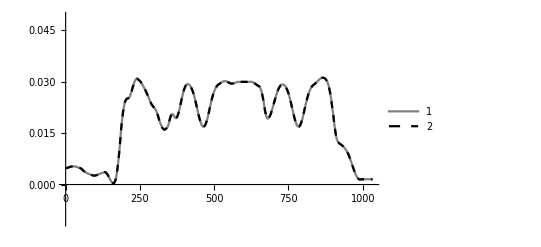

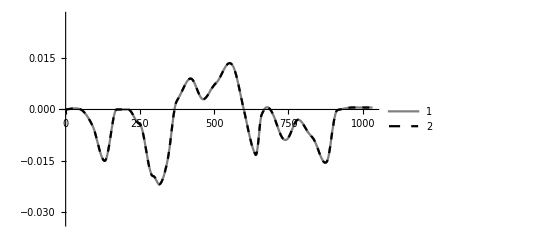

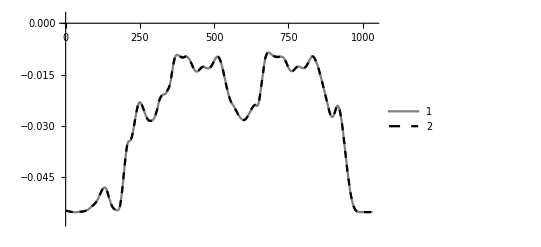

```mathematica
plot = {comLog, comSensor};
ListPointPlot3D[plot]
r = 0.03
mx= Mean[plot[[All,All,1]][[1]]];
my= Mean[plot[[All,All,2]][[1]]];
mz= Mean[plot[[All,All,3]][[1]]];

(*ListLinePlot[plot[[All,All,1]],PlotRange->{mx-r,mx+r},PlotLegends->Automatic,PlotMarkers->Automatic]*)
ListLinePlot[plot[[All,All,1]],PlotRange->{mx-r,mx+r},PlotLegends->Placed[{"X_CoM from Model","X_CoM from Aldebaran API"},Above],PlotStyle->{{Gray,Thick},{Dashed,Black}}]
ListLinePlot[plot[[All,All,2]],PlotRange->{my-r,my+r},PlotLegends->Placed[{"Y_CoM from Model","Y_CoM from Aldebaran API"},Above],PlotStyle->{{Gray,Thick},{Dashed,Black}}]
ListLinePlot[plot[[All,All,3]],PlotRange->{mz-r,mz+r},PlotLegends->Placed[{"Z_CoM from Model","Z_CoM from Aldebaran API"},Above],PlotStyle->{{Gray,Thick},{Dashed,Black}}]
Manipulate[
i=Floor[j];
setTheta[i];

head = Graphics3D[{Thick,Line[{{0,0,0},THD3toTorso[[1;;3,4]]}]}];

righthand= Graphics3D[{Thick,Line[{{0,0,0},{0,0,0.100},TRH1toTorso[[1;;3,4]],TRH5toTorso[[1;;3,4]],TRH6toTorso[[1;;3,4]]}]}];

lefthand=Graphics3D[{Thick,Line[{{0,0,0},{0,0,0.100},TLH1toTorso[[1;;3,4]],TLH5toTorso[[1;;3,4]],TLH6toTorso[[1;;3,4]]}]}];

rightleg = Graphics3D[{Thick,Line[{{0,0,0},TRL1toTorso[[1;;3,4]],TRL4toTorso[[1;;3,4]],TRL6toTorso[[1;;3,4]],TRL7toTorso[[1;;3,4]]}]}];

leftleg = Graphics3D[{Thick,Line[{{0,0,0},TLL1toTorso[[1;;3,4]],TLL4toTorso[[1;;3,4]],TLL6toTorso[[1;;3,4]],TLL7toTorso[[1;;3,4]]}]}];

rightlegground = Graphics3D[{Yellow, Polygon[{TRL7toTorso.{0,0.05,0.05,1},TRL7toTorso.{0,-0.05,0.05,1},TRL7toTorso.{0,-0.05,-0.05,1},TRL7toTorso.{0,0.05,-0.05,1}}[[All,1;;3]]]}];

leftlegground = Graphics3D[{Yellow, Polygon[{TLL7toTorso.{0,0.05,0.05,1},TLL7toTorso.{0,-0.05,0.05,1},TLL7toTorso.{0,-0.05,-0.05,1},TLL7toTorso.{0,0.05,-0.05,1}}[[All,1;;3]]]}];

comLogSphere=Graphics3D[{Orange,Sphere[comLog[[i]],0.005]}];
comSensorSphere=Graphics3D[{Blue,Sphere[comSensor[[i]],0.005]}];

comHDLogSphere=Graphics3D[{Orange,Sphere[comHDLog[[i]],0.004]}];
comHDSensorSphere=Graphics3D[{Blue,Sphere[comHDSensor[[i]],0.004]}];

comRHLogSphere=Graphics3D[{Orange,Sphere[comRHLog[[i]],0.004]}];
comLHLogSphere=Graphics3D[{Orange,Sphere[comLHLog[[i]],0.004]}];

comRHSensorSphere=Graphics3D[{Blue,Sphere[comRHSensor[[i]],0.004]}];
comLHSensorSphere=Graphics3D[{Blue,Sphere[comLHSensor[[i]],0.004]}];

comRLLogSphere=Graphics3D[{Orange,Sphere[comRLLog[[i]],0.004]}];
comLLLogSphere=Graphics3D[{Orange,Sphere[comLLLog[[i]],0.004]}];

comRLSensorSphere=Graphics3D[{Blue,Sphere[comRLSensor[[i]],0.004]}];
comLLSensorSphere=Graphics3D[{Blue,Sphere[comLLSensor[[i]],0.004]}];

(*Show[{head,righthand,lefthand,rightleg,leftleg,comLogSphere,comRLLogSphere,comLLLogSphere,comRHLogSphere,comLHLogSphere},Boxed->False,Background->RGBColor[0.84,0.92,1.]]*)

Show[{head,righthand,lefthand,rightleg,leftleg,comLogSphere,comSensorSphere,comHDLogSphere,comHDSensorSphere,comRLLogSphere,comLLLogSphere,comRHLogSphere,comLHLogSphere,comRHSensorSphere,comLHSensorSphere,comRLSensorSphere,comLLSensorSphere,rightlegground,leftlegground},Boxed->False,Background->RGBColor[0.84,0.92,1.]]

,{j,1,lenData}]
```

```mathematica
Show[%243,AxesStyle->Black]
```

-Graphics3D-

```mathematica
Show[%252,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.71]]]
```

-Graphics3D-

```mathematica
Show[%253,ImageSize->Large]
```

-Graphics3D-

```mathematica
Show[%254,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%256,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%256,ImageSize→Large]

```mathematica
Export["C:\\Users\\Pourya\\Dropbox\\PSH-MJ\\Whole_Body\\CoM_Verification\\CoM_Verification_3.eps",%257,"EPS"]
```

Export::nodir: Directory "C:\\Users\\Pourya\\Dropbox\\PSH-MJ\\Whole_Body\\CoM_Verification\\" does not exist.

Export::noopen: Cannot open "C:\\Users\\Pourya\\Dropbox\\PSH-MJ\\Whole_Body\\CoM_Verification\\CoM_Verification_3.eps".

$Failed

```mathematica
Export["C:\\Users\\Pourya\\Dropbox\\PSH-MJ\\Whole_Body\\CoM_Verification\\.dxf",%257,"DXF"]
```

Export::nodir: Directory "C:\\Users\\Pourya\\Dropbox\\PSH-MJ\\Whole_Body\\CoM_Verification\\" does not exist.

OpenWrite::noopen: Cannot open "C:\\Users\\Pourya\\Dropbox\\PSH-MJ\\Whole_Body\\CoM_Verification\\.dxf".

$Failed